```mathematica
SetOptions[EvaluationNotebook[],  CommonDefaultFormatTypes -> {"Output" -> StandardForm}]
```

```mathematica
Integrate[(Γ m)/((x-m^2)^2+(Γ m)^2), {x, a, b}, Assumptions->{m∈Reals, m>0, Γ∈Reals, Γ>0, b>a}]
```

-ArcCot[(m Γ)/(a-m^2)]+ArcCot[(m Γ)/(b-m^2)]

```mathematica
f[t_] := (Re[Q]+ⅈ Im[Q])/(t-m^2+ⅈ Γ m)+(Re[Q]-ⅈ Im[Q])/(t-m^2-ⅈ Γ m)
fint = Integrate[f[t], {t, a, b}, Assumptions->{Q∈Complexes, m∈PositiveReals, m>0, Γ∈PositiveReals, Γ>0, a∈Reals, b∈Reals, b>a, a<m^2, b>m^2}]
```

2 (π+ArcTan[(m Γ)/(a-m^2)]+ArcTan[(m Γ)/(-b+m^2)]) Im[Q]+Log[((b-m^2)^2+m^2 Γ^2)/((a-m^2)^2+m^2 Γ^2)] Re[Q]

Setting  parameters

```mathematica
mi = 100;
mj = 100;
mA = 1000;
GA = 1;
```

Setting up integration boundary functions

```mathematica
p[s_] := Sqrt[(s-(mi-mj)^2)(s-(mi+mj)^2)]
t1[s_] := (mi^2+mj^2-s)/2+Sqrt[s]*p[s]
t0[s_] := (mi^2+mj^2-s)/2-Sqrt[s]*p[s]
```

Actual integral as function of integration boundaries

```mathematica
F[s_] := Integrate[(GA mA)/((x-mA^2)^2 + GA^2mA^2), {x, t0[s], t1[s]}]
Fanalytic = 1/2 Integrate[(Re[Q]+ⅈ Im[Q])/(t-m^2+ⅈ Γ m)+(Re[Q]-ⅈ Im[Q])/(t-m^2-ⅈ Γ m), {t, a, b}, Assumptions->{Q∈Complexes, m∈PositiveReals, m>0, Γ∈PositiveReals, Γ>0, a∈Reals, b∈Reals, b>a, a<m^2, b>m^2}] //
	ReplaceAll[#, {Re[Q]->0, Im[Q]->1, m->mA, Γ->GA}]&
FPW[s_] := Piecewise[{{ArcTan[(GA mA)/(t0[s^2]-mA^2)]-ArcTan[(GA mA)/(t1[s^2]-mA^2)], t1[s^2]<0}, {ArcTan[(t1[s^2]-mA^2)/(GA mA)] - ArcTan[(t0[s^2]-mA^2)/(GA mA)], t1[s^2]>=0}}]
```

π+ArcTan[1000/(-1000000+a)]+ArcTan[1000/(1000000-b)]

Plotting “analytic” result of integral vs. actual integral value as function of integration boundaries

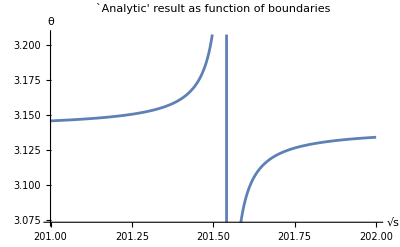

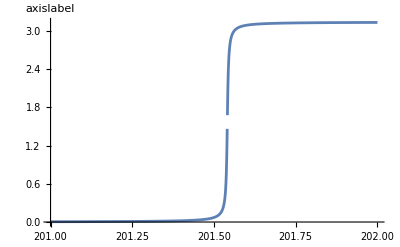

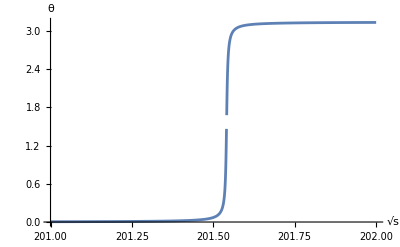

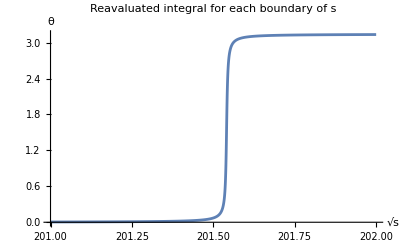

```mathematica
intargs = {s, 1.005(mi+mj), 1.01(mi+mj)};
axeslabel = {"√s", "θ"};
Plot[ReplaceAll[Fanalytic, {a->t0[s^2], b->t1[s^2]}], intargs, PlotLabel->"`Analytic' result as function of boundaries", AxesLabel->axeslabel]
(*Plot[2 ArcTan[(10/(-1+t0[s])+10/(1-t1[s]))/(1-10/(-1+t0[s])10/(1-t1[s]))],  {s, (mi+mj)^2, 1.01(mi+mj)^2}, PlotLabel->"`Analytic' result combining the arctan functions", AxesLabel->{"s", "θ"}]*)
Plot[ArcTan[(t1[s^2]-mA^2)/(GA mA)] - ArcTan[(t0[s^2]-mA^2)/(GA mA)], intargs, AxesLabel->axislabel]
Plot[FPW[s], intargs, AxesLabel->axeslabel]
Plot[F[s^2], intargs, PlotLabel->"Reavaluated integral for each boundary of s", AxesLabel->axeslabel]
```

```mathematica
Integrate[x^3/(x^2+c^2), {x, a, b}, Assumptions->{a∈Reals, b∈Reals, b>a, c∈Reals, c!=0}]
```

1/2 (-a^2+b^2+c^2 Log[(a^2+c^2)/(b^2+c^2)])

```mathematica
Plot[{t0[s], t1[s]}, {s, (mi+mj)^2, 13600^2}, Filling -> {1 -> {2}}]
```

Plot::plln: Limiting value (mi+mj)^2 in {s,(mi+mj)^2,184960000} is not a machine-sized real number.

Plot[{t0[s],t1[s]},{s,(mi+mj)^2,13600^2}]